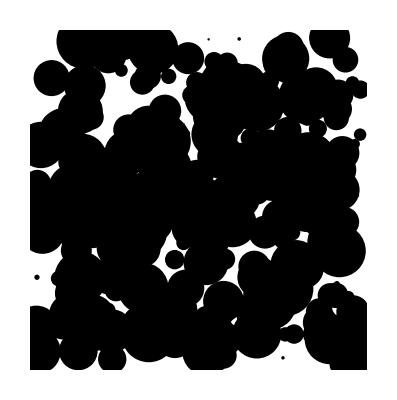

```mathematica
Graphics[ 
Table[
{
PointSize[RandomReal[{0,0.1}]],
Point[RandomReal[1,{2}]]
},
{300}
]
]
```

```mathematica
Table[
{
Hue[0.5*dat[[i,4]]]
PointSize[0.1 * dat[[i,3]]],
Point[dat[[i,1;;2]]]
},
{i,1,3}
]
```

{{Hue[0.5] PointSize[0.3],Point[{-0.5,6.5}]},{Hue[0.5] PointSize[0.5],Point[{-0.5,7.5}]},{Hue[0.5] PointSize[0.2],Point[{-1,-8.5}]}}

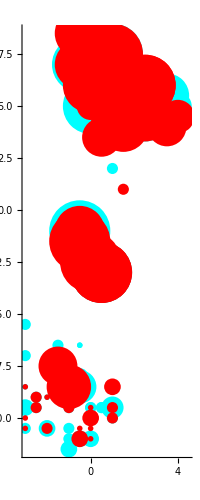

```mathematica
Graphics[
Table[
{
Hue[0.5* dat[[i,4]]],
PointSize[0.01 * dat[[i,3]]],
Point[dat[[i,1;;2]]]
},
{i,1,133}
],
Axes->True,
AxesOrigin->{-4,-12}
]
```

```mathematica
dat[[1,1]]
```

-0,500000000000000

```mathematica
Table[
{
PointSize[RandomReal[{0,0.1}]],
Point[RandomReal[1,{2}]]
},
{5}
]
```

{{PointSize[0.058338],Point[{0.760477,0.539849}]},{PointSize[0.0552024],Point[{0.0733525,0.25018}]},{PointSize[0.0703243],Point[{0.441123,0.832932}]},{PointSize[0.0772943],Point[{0.51036,0.415785}]},{PointSize[0.0331086],Point[{0.96971,0.901349}]}}

```mathematica
dat = {{-0.5,6.5,3,1},{-0.5,7.5,5,1},{-1,-8.5,2,1},{1,-9.5,3,1},{0.5,8,8,1},{0,-8.5,1,1},{3.5,5,3,1},{0,-9.5,2,1},{0.5,5.5,10,1},{-0.5,-11,3,1},{-1.5,-7.5,6,1},{-0.5,8.5,8,1},{3.5,4,6,1},{-0.5,6,1,1},{1,6,10,1},{2.5,6,10,1},{-2,-10.5,3,1},{0,4,1,1},{3.5,5.5,8,1},{-3,-10.5,2,1},{0,5,2,1},{1,7.5,11,1},{-2.5,-9,2,1},{-0.5,7,10,1},{0.5,6,10,1},{4.5,4.5,1,1},{-0.5,-8.5,6,1},{-1.5,-7,2,1},{2,4.5,8,1},{2,4.5,8,1},{-2,-9,1,1},{1.5,4.5,9,1},{1.5,4.5,10,1},{-2.5,-9.5,2,1},{-1,-11.5,3,1},{1,2,2,1},{0.5,3.5,2,1},{1.5,1,1,1},{0,-10,1,1},{1,5.5,9,1},{-1,-11,2,1},{2.5,4.5,9,1},{-3,-9.5,3,1},{-1,-9.5,2,1},{1.5,5,1,1},{0,-9.5,2,1},{1.5,6,8,1},{0.5,-3,11,1},{0,-11,3,1},{2,6.5,2,1},{-3,-8.5,1,1},{1,-10,2,1},{2.5,6.5,2,1},{2,5.5,6,1},{0.5,-9.5,2,1},{2,5.5,1,1},{0.5,-9.5,2,1},{-0.5,-1,11,1},{1,-9.5,4,1},{4,5,5,1},{0,6,6,1},{-0.5,-8,3,1},{-3,-5.5,2,1},{-1,-10.5,2,1},{-1.5,-6.5,2,1},{3,5.5,8,1},{-3,-7,2,1},{0,5,10,1},{1,6.5,6,1},{-0.5,-6.5,1,1},{-0.5,-6.5,1,1},{1,6.5,9,1},{1.5,4,9,2},{-0.5,6.5,2,2},{-1,-9.5,1,2},{-1,-8.5,8,2},{-0.5,7.5,6,2},{-3,-8.5,1,2},{4,4.5,6,2},{0,-10,3,2},{4,4.5,3,2},{0,-10,2,2},{1,-9.5,2,2},{-2,-10.5,2,2},{0.5,5.5,2,2},{0,-9.5,1,2},{-0.5,-11,3,2},{-0.5,8.5,9,2},{-1.5,-7.5,7,2},{1,4,8,2},{3.5,4,7,2},{-0.5,6,1,2},{1,6,8,2},{1,6,11,2},{2.5,6,11,2},{2.5,6,11,2},{0,-10.5,1,2},{-2,-10.5,1,2},{0,5,4,2},{-3,-10.5,1,2},{1,7.5,11,2},{-2.5,-9,2,2},{-0.5,7,9,2},{4.5,4.5,2,2},{-0.5,-8.5,4,2},{2,4.5,8,2},{0.5,7,8,2},{-0.5,-10.5,1,2},{-2,-9,1,2},{1.5,4.5,10,2},{-2.5,-9.5,2,2},{0.5,3.5,7,2},{1.5,1,2,2},{0,-2.5,11,2},{-0.5,-1.5,11,2},{2.5,4.5,9,2},{3.5,3.5,1,2},{-1,-9.5,2,2},{0,7,8,2},{-3,-10,1,2},{0.5,-3,11,2},{0.5,-3,11,2},{2,6.5,1,2},{0,-11,1,2},{2.5,6.5,1,2},{1,-10,2,2},{2,5.5,1,2},{-0.5,-1,9,2},{4,5,1,2},{1,-9.5,1,2},{0,6,10,2},{1,-8.5,3,2},{0,5,5,2}}
```

{{-0.5,6.5,3,1},{-0.5,7.5,5,1},{-1,-8.5,2,1},{1,-9.5,3,1},{0.5,8,8,1},{0,-8.5,1,1},{3.5,5,3,1},{0,-9.5,2,1},{0.5,5.5,10,1},{-0.5,-11,3,1},{-1.5,-7.5,6,1},{-0.5,8.5,8,1},{3.5,4,6,1},{-0.5,6,1,1},{1,6,10,1},{2.5,6,10,1},{-2,-10.5,3,1},{0,4,1,1},{3.5,5.5,8,1},{-3,-10.5,2,1},{0,5,2,1},{1,7.5,11,1},{-2.5,-9,2,1},{-0.5,7,10,1},{0.5,6,10,1},{4.5,4.5,1,1},{-0.5,-8.5,6,1},{-1.5,-7,2,1},{2,4.5,8,1},{2,4.5,8,1},{-2,-9,1,1},{1.5,4.5,9,1},{1.5,4.5,10,1},{-2.5,-9.5,2,1},{-1,-11.5,3,1},{1,2,2,1},{0.5,3.5,2,1},{1.5,1,1,1},{0,-10,1,1},{1,5.5,9,1},{-1,-11,2,1},{2.5,4.5,9,1},{-3,-9.5,3,1},{-1,-9.5,2,1},{1.5,5,1,1},{0,-9.5,2,1},{1.5,6,8,1},{0.5,-3,11,1},{0,-11,3,1},{2,6.5,2,1},{-3,-8.5,1,1},{1,-10,2,1},{2.5,6.5,2,1},{2,5.5,6,1},{0.5,-9.5,2,1},{2,5.5,1,1},{0.5,-9.5,2,1},{-0.5,-1,11,1},{1,-9.5,4,1},{4,5,5,1},{0,6,6,1},{-0.5,-8,3,1},{-3,-5.5,2,1},{-1,-10.5,2,1},{-1.5,-6.5,2,1},{3,5.5,8,1},{-3,-7,2,1},{0,5,10,1},{1,6.5,6,1},{-0.5,-6.5,1,1},{-0.5,-6.5,1,1},{1,6.5,9,1},{1.5,4,9,2},{-0.5,6.5,2,2},{-1,-9.5,1,2},{-1,-8.5,8,2},{-0.5,7.5,6,2},{-3,-8.5,1,2},{4,4.5,6,2},{0,-10,3,2},{4,4.5,3,2},{0,-10,2,2},{1,-9.5,2,2},{-2,-10.5,2,2},{0.5,5.5,2,2},{0,-9.5,1,2},{-0.5,-11,3,2},{-0.5,8.5,9,2},{-1.5,-7.5,7,2},{1,4,8,2},{3.5,4,7,2},{-0.5,6,1,2},{1,6,8,2},{1,6,11,2},{2.5,6,11,2},{2.5,6,11,2},{0,-10.5,1,2},{-2,-10.5,1,2},{0,5,4,2},{-3,-10.5,1,2},{1,7.5,11,2},{-2.5,-9,2,2},{-0.5,7,9,2},{4.5,4.5,2,2},{-0.5,-8.5,4,2},{2,4.5,8,2},{0.5,7,8,2},{-0.5,-10.5,1,2},{-2,-9,1,2},{1.5,4.5,10,2},{-2.5,-9.5,2,2},{0.5,3.5,7,2},{1.5,1,2,2},{0,-2.5,11,2},{-0.5,-1.5,11,2},{2.5,4.5,9,2},{3.5,3.5,1,2},{-1,-9.5,2,2},{0,7,8,2},{-3,-10,1,2},{0.5,-3,11,2},{0.5,-3,11,2},{2,6.5,1,2},{0,-11,1,2},{2.5,6.5,1,2},{1,-10,2,2},{2,5.5,1,2},{-0.5,-1,9,2},{4,5,1,2},{1,-9.5,1,2},{0,6,10,2},{1,-8.5,3,2},{0,5,5,2}}